## Load matex and setup font

```mathematica
<<MaTeX`
font={BaseStyle->{FontFamily->"Times New Roman",FontSize->12},AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Times New Roman",FontSize-> 12}};
```

## Simple plot

```mathematica
pl=Plot[{ArcTan[x],Sin[x]},{x,-10,10},
Evaluate@font,
Frame->True,Axes->False,FrameTicks->{{{-π/2,-1,0,1,π/2},None},{Range[-10,10,2],None}},
FrameLabel->None,PlotRange->{-1.9,1.9},
(*simplest way to put labels: FrameLabel->MaTeX/@{"x","\\arctan(x)"}, but the position is not customizable. For that we use Epilog*)

(*increase border and add the ability to write outside of the plot (sometimes lines of plot can go beyond, which needs to be fixed with anothed hacks)*)
ImagePadding->{{31,3},{40,7}},PlotRangeClipping->False,
Epilog->{Text[MaTeX["x"],{0,-2.4}],Text[Rotate[MaTeX["f(x)"],π/2],{-12,0}]},

PlotStyle->{Black, {Blue,Dashed}},
GridLines->{None, {-1,0,1}}
]
```

-Graphics-

## Density Plot

```mathematica
bar=BarLegend["TemperatureMap",LegendMarkerSize->{10,220},LegendLayout->"Column",Evaluate@font]
```

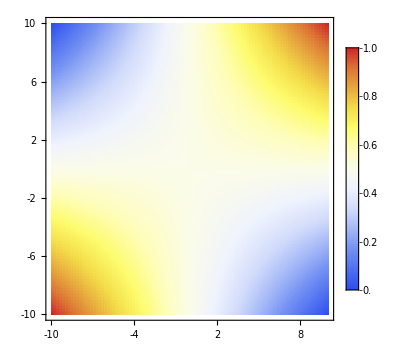

```mathematica
dens=DensityPlot[x*y,{x,-10,10},{y,-10,10},
Evaluate@font,
PlotPoints->100,Exclusions->None,
PlotRange->All,
ColorFunction->"Temperature",PlotLegends->None,
FrameTicks->{{Range[-10,10,2],None},{Range[-10,10,2],None}},
FrameLabel->MaTeX/@{"x","\\frac{\\beta}{N}"},
AspectRatio->1,
ImagePadding->{{61,40},{40,7}},PlotRangeClipping->False,Epilog->Inset[bar,{12,-1}],
ImageSize->350
]
```

## Multiple Plots

https : // resources . wolframcloud . com/FunctionRepository/resources/PlotGrid/

```mathematica
ResourceFunction["PlotGrid"];
```

```mathematica
ResourceFunction["PlotGrid"][{{pl},{dens}},
Epilog->Inset["aaaaaaa",{0.5,0.6}]
(*, Spacings->15*)
]
```

-Graphics-